```mathematica
MakeBoxes[Σd,StandardForm]:=SubscriptBox["Σ","d"];MakeExpression[SubscriptBox["Σ","d"],StandardForm]:=MakeExpression["Σd",StandardForm];
MakeBoxes[Σod,StandardForm]:=SubscriptBox["Σ","od"];MakeExpression[SubscriptBox["Σ","od"],StandardForm]:=MakeExpression["Σod",StandardForm];
MakeBoxes[Σtd,StandardForm]:=SubscriptBox["Σ","td"];MakeExpression[SubscriptBox["Σ","td"],StandardForm]:=MakeExpression["Σtd",StandardForm];
MakeBoxes[Σtod,StandardForm]:=SubscriptBox["Σ","tod"];MakeExpression[SubscriptBox["Σ","tod"],StandardForm]:=MakeExpression["Σtod",StandardForm];
MakeBoxes[Φd,StandardForm]:=SubscriptBox["Φ","d"];MakeExpression[SubscriptBox["Φ","d"],StandardForm]:=MakeExpression["Φd",StandardForm];
MakeBoxes[Φod,StandardForm]:=SubscriptBox["Φ","od"];MakeExpression[SubscriptBox["Φ","od"],StandardForm]:=MakeExpression["Φod",StandardForm];
MakeBoxes[Φbd,StandardForm]:=SubscriptBox["Φ","bd"];MakeExpression[SubscriptBox["Φ","bd"],StandardForm]:=MakeExpression["Φbd",StandardForm];
MakeBoxes[Φbod,StandardForm]:=SubscriptBox["Φ","bod"];MakeExpression[SubscriptBox["Φ","bod"],StandardForm]:=MakeExpression["Φbod",StandardForm];

MakeBoxes[Σd,TraditionalForm]:=SubscriptBox["Σ","d"];MakeExpression[SubscriptBox["Σ","d"],TraditionalForm]:=MakeExpression["Σd",TraditionalForm];
MakeBoxes[Σod,TraditionalForm]:=SubscriptBox["Σ","od"];MakeExpression[SubscriptBox["Σ","od"],TraditionalForm]:=MakeExpression["Σod",TraditionalForm];
MakeBoxes[Σtd,TraditionalForm]:=SubscriptBox["Σ","td"];MakeExpression[SubscriptBox["Σ","td"],TraditionalForm]:=MakeExpression["Σtd",TraditionalForm];
MakeBoxes[Σtod,TraditionalForm]:=SubscriptBox["Σ","tod"];MakeExpression[SubscriptBox["Σ","tod"],TraditionalForm]:=MakeExpression["Σtod",TraditionalForm];
MakeBoxes[Φd,TraditionalForm]:=SubscriptBox["Φ","d"];MakeExpression[SubscriptBox["Φ","d"],TraditionalForm]:=MakeExpression["Φd",TraditionalForm];
MakeBoxes[Φod,TraditionalForm]:=SubscriptBox["Φ","od"];MakeExpression[SubscriptBox["Φ","od"],TraditionalForm]:=MakeExpression["Φod",TraditionalForm];
MakeBoxes[Φbd,TraditionalForm]:=SubscriptBox["Φ","bd"];MakeExpression[SubscriptBox["Φ","bd"],TraditionalForm]:=MakeExpression["Φbd",TraditionalForm];
MakeBoxes[Φbod,TraditionalForm]:=SubscriptBox["Φ","bod"];MakeExpression[SubscriptBox["Φ","bod"],TraditionalForm]:=MakeExpression["Φbod",TraditionalForm];
```

```mathematica
a = (I ω - Σd);
b = (-Φd );
c = (I ω - Σtd);
(*d = (-λ - Σod);*)
(*d = (-λ - Σod Exp[I θ]);*)
d = ( - Σod );
e = (-Φod);
(*f = (λ Exp[-I θ] - Σtod);*)
(*f = (λ- Σtod Exp[-I θ]);*)
f = (- Σtod);
g = -(Φbd);
h = -(Φbod);
(*A = {{a,b Exp[I θ]},{g Exp[-I θ],c}};
B = {{d Exp[I θ],e},{h,f Exp[-I θ]}};
L = {{d Exp[-I θ],e},{h,f Exp[I θ]}};
M = {{a,b Exp[-I θ]},{g Exp[I θ],c}};*)
(*A = {{a,b },{g ,c}};
B = {{d ,e},{h,f }};
L = {{d ,e},{h,f }};
M = {{a,b },{g ,c}};*)
(*A = {{a,b },{g ,c}};
B = {{-λ Exp[-I θ]+ d Exp[-I θ] ,e Exp[I θ]},{h Exp[-I θ],λ Exp[I θ]+ f Exp[I θ] }};
L = {{-λ Exp[I θ]+ d Exp[I θ],e Exp[I θ]},{h Exp[-I θ],λ Exp[-I θ] + f Exp[-I θ] }};
M = {{a,b Exp[2 I θ] },{g Exp[- 2I θ],c}};*)
(*A = {{a,b },{g ,c}};
B = {{-λ + d Exp[-I θ] ,e Exp[I θ]},{h Exp[-I θ],λ + f Exp[I θ] }};
L = {{-λ + d Exp[I θ],e Exp[I θ]},{h Exp[-I θ],λ  + f Exp[-I θ] }};
M = {{a,b Exp[2 I θ] },{g Exp[- 2I θ],c}};*)
(*A = {{a,b },{g ,c}};
B = {{-λ Exp[-I θ]+d ,e},{h,λ Exp[I θ]+f }};
L = {{-λ Exp[I θ]+ d  ,e},{h,λ Exp[-I θ]+ f}};
M = {{a,b },{g ,c}};*)
A = {{a,b },{g ,c}};
B = {{-λ + d  ,e },{h ,λ + f  }};
L = {{-λ + d ,e },{h ,λ  + f  }};
M = {{a,b Exp[2 I θ] },{g Exp[- 2I θ],c}};
Ginv = ArrayFlatten[{{A,B},{L,M}}];
Ginv//MatrixForm
asslist = {Element[ω,Reals],Element[λ,Reals],λ>0,Element[θ,Reals]};
redoneside  = {λ->0, Φod->0,Σtod->0,Σod->0, Φbod->0};
strreprule = {"(0,1)"->"1j", "Σd"-> "SigmaDomega","Σod"-> "SigmaODomega", "Φd"-> "PhiDomega","Φod"-> "PhiODomega","λ"->"lamb","ω"->"omega", "Im"->"np.imag" ,"(0,-1)"->"-1j","Cos"->"np.cos","Abs"->"np.abs", "θ"-> "theta", "Re"->"np.real","(0,2)"->"2j"};
repst = {Σtd-> -Conjugate@Σd, Σtod-> -Conjugate@Σod, Φbd->Conjugate@Φd, Φbod->Conjugate@Φod};
redMET = {Φd -> 0, Φod -> 0, Φbd -> 0, Φbod -> 0};
spsymmreprule = {Conjugate[Σod]->Σod, Conjugate[Σd]-> -Σd};
detGinv = FullSimplify[Det[Ginv],Assumptions->asslist];
detGinv
```

(-Σ_d+ⅈ ω | -Φ_d | -λ-Σ_od | -Φ_od
-Φ_bd | -Σ_td+ⅈ ω | -Φ_bod | λ-Σ_tod
-λ-Σ_od | -Φ_od | -Σ_d+ⅈ ω | -ⅇ^(2 ⅈ θ) Φ_d
-Φ_bod | λ-Σ_tod | -ⅇ^(-2 ⅈ θ) Φ_bd | -Σ_td+ⅈ ω)

λ^4+Σ_d^2 Σ_td^2-Σ_od^2 Σ_td^2+2 λ^3 (Σ_od-Σ_tod)-Σ_d^2 Σ_tod^2+Σ_od^2 Σ_tod^2-2 Σ_d Σ_td Φ_bd Φ_d+Σ_od Σ_td Φ_bod Φ_d+Σ_d Σ_tod Φ_bod Φ_d+Φ_bd^2 Φ_d^2+Σ_od Σ_td Φ_bd Φ_od+Σ_d Σ_tod Φ_bd Φ_od-2 Σ_d Σ_td Φ_bod Φ_od-2 Σ_od Σ_tod Φ_bod Φ_od+Φ_bod^2 Φ_od^2+2 λ (-Σ_od^2 Σ_tod+Σ_tod (-Φ_bod Φ_od+(Σ_d-ⅈ ω)^2)+Σ_od (Σ_tod^2+Φ_bod Φ_od-(Σ_td-ⅈ ω)^2))-ⅈ (2 Σ_d^2 Σ_td-2 Σ_od^2 Σ_td+2 Σ_d Σ_td^2-2 Σ_d Σ_tod^2-2 Σ_d Φ_bd Φ_d-2 Σ_td Φ_bd Φ_d+Σ_od Φ_bod Φ_d+Σ_tod Φ_bod Φ_d+(Σ_od+Σ_tod) Φ_bd Φ_od-2 (Σ_d+Σ_td) Φ_bod Φ_od) ω+(-Σ_d^2+Σ_od^2-4 Σ_d Σ_td-Σ_td^2+Σ_tod^2+2 Φ_bd Φ_d+2 Φ_bod Φ_od) ω^2+2 ⅈ (Σ_d+Σ_td) ω^3+ω^4-ⅇ^(2 ⅈ θ) Φ_d (Σ_od Σ_tod Φ_bd-Σ_od Σ_td Φ_bod-Σ_d Σ_tod Φ_bod+Φ_bod^2 Φ_d+ⅈ (Σ_od+Σ_tod) Φ_bod ω)+ⅇ^(-2 ⅈ θ) Φ_bd (-Σ_od Σ_tod Φ_d+Σ_od Σ_td Φ_od+Σ_d Σ_tod Φ_od-Φ_bd Φ_od^2-ⅈ (Σ_od+Σ_tod) Φ_od ω)+λ^2 (-Σ_d^2+Σ_od^2-Σ_td^2-4 Σ_od Σ_tod+Σ_tod^2+2 Φ_bod Φ_od+2 ⅈ (Σ_d+Σ_td) ω+2 ω^2)-2 ⅇ^(-ⅈ θ) λ (Σ_d-Σ_td) (ⅇ^(2 ⅈ θ) Φ_bod Φ_d+Φ_bd Φ_od) Cos[θ]+2 λ (λ+Σ_od-Σ_tod) Φ_bd Φ_d Cos[2 θ]

```mathematica
scFE =FullSimplify[detGinv/.repst/.{Φod->0, Φbod -> 0}] (*remember to take -log of this *)
```

(λ+Σ_d+Σ_od-ⅈ ω) (λ-Σ_d+Σ_od+ⅈ ω) (λ^2+ω^2)+2 ⅈ Σ_d ω Abs[Σ_d]^2+Abs[Σ_d]^4+2 λ Σ_od Abs[Σ_od]^2+Abs[Σ_od]^4+Abs[Φ_d]^4-((λ+Σ_od)^2+2 ⅈ Σ_d ω+ω^2) Conjugate[Σ_d]^2+(λ^2+2 λ Σ_od-(Σ_d-ⅈ ω)^2) Conjugate[Σ_od]^2+2 Conjugate[Σ_d] (-ⅈ ω ((λ+Σ_od)^2+2 ⅈ Σ_d ω+ω^2)+Σ_d Φ_d Conjugate[Φ_d])+2 Conjugate[Σ_od] (λ (λ^2+2 λ Σ_od-(Σ_d-ⅈ ω)^2)+Σ_od Φ_d Conjugate[Φ_d] Cos[2 θ])+2 Φ_d Conjugate[Φ_d] (λ (λ+Σ_od+Conjugate[Σ_od]) Cos[2 θ]+ω (2 ⅈ Σ_d+ω-2 ⅈ Re[Σ_d]))

```mathematica
(*(Simplify[scFE ,Assumptions->asslist]/.{(Sin[θ/2])^2->((1-Cos[θ])/2)} //Curry[Coefficient][Cos[θ]])/.spsymmreprule//Curry[Simplify][Assumptions->asslist]//TeXForm*)
(Simplify[scFE ,Assumptions->asslist]/.{(Sin[θ/2])^2->((1-Cos[θ])/2)} //Curry[Coefficient][Cos[2θ]])//Simplify
```

2 (λ+Σ_od) Φ_d (λ+Conjugate[Σ_od]) Conjugate[Φ_d]

```mathematica
(*/.{Conjugate[Σd] -> -Σd,Conjugate[Σod] -> Σod }*)
(*Shortest["Conjugate("~~x___~~")"] -> "np.conj("~~x~~")"*)
scFE//FortranForm//ToString//StringReplace[strreprule]//StringReplace[Shortest["Conjugate("~~x___~~")"] -> "np.conj("~~x~~")"]
```

(lamb + SigmaDomega + SigmaODomega - 1j*omega)*(lamb - SigmaDomega + SigmaODomega + 1j*omega)*(lamb**2 + omega**2) + 2j*SigmaDomega*omega*np.abs(SigmaDomega)**2 + np.abs(SigmaDomega)**4 + 2*lamb*SigmaODomega*np.abs(SigmaODomega)**2 + np.abs(SigmaODomega)**4 + np.abs(PhiDomega)**4 - ((lamb + SigmaODomega)**2 + 2j*SigmaDomega*omega + omega**2)*np.conj(SigmaDomega)**2 + (lamb**2 + 2*lamb*SigmaODomega - (SigmaDomega - 1j*omega)**2)*np.conj(SigmaODomega)**2 + 2*np.conj(SigmaDomega)*(-1j*omega*((lamb + SigmaODomega)**2 + 2j*SigmaDomega*omega + omega**2) + SigmaDomega*PhiDomega*np.conj(PhiDomega)) + 2*np.conj(SigmaODomega)*(lamb*(lamb**2 + 2*lamb*SigmaODomega - (SigmaDomega - 1j*omega)**2) + SigmaODomega*PhiDomega*np.conj(PhiDomega)*np.cos(2*theta)) + 2*PhiDomega*np.conj(PhiDomega)*(lamb*(lamb + SigmaODomega + np.conj(SigmaODomega))*np.cos(2*theta) + omega*(2j*SigmaDomega + omega - 2j*np.real(SigmaDomega)))

```mathematica
metFE = FullSimplify[detGinv /.repst /.redMET /.{Conjugate[Σod]->Σod, Conjugate[Σd]-> -Σd}] (*Det G should not depend on theta upon turning off superconductivity*)
(*FullSimplify[D[FullSimplify[detGinv /.repst /.redMET],θ]]*)
```

(λ+Σ_d+Σ_od-ⅈ ω)^2 (λ-Σ_d+Σ_od+ⅈ ω)^2

```mathematica
metFE /( metFE/.θ->0)  //Simplify
```

1

```mathematica
Series[FullSimplify[Log[metFE /(metFE/.θ->0)]],{λ,0,2}]
```

0

```mathematica
diffFE = FullSimplify[scFE /.{Conjugate[Σod]->Σod, Conjugate[Σd]-> -Σd},Assumptions->asslist]
```

λ^4-2 λ^2 Σ_d^2+4 λ^3 Σ_od-4 λ Σ_d^2 Σ_od+6 λ^2 Σ_od^2-2 Σ_d^2 Σ_od^2+2 λ Σ_od^3+2 ⅈ Σ_d (-Σ_d^2+2 (λ+Σ_od)^2) ω+2 (-3 Σ_d^2+(λ+Σ_od)^2) ω^2+4 ⅈ Σ_d ω^3+ω^4+2 ⅈ Σ_d ω Abs[Σ_d]^2+Abs[Σ_d]^4+2 λ Σ_od Abs[Σ_od]^2+Abs[Σ_od]^4+Abs[Φ_d]^4+2 Φ_d Conjugate[Φ_d] (-(Σ_d-ⅈ ω)^2+(λ+Σ_od)^2 Cos[2 θ]-2 ⅈ ω Re[Σ_d])

```mathematica
ij = FullSimplify[D[FullSimplify[detGinv /.repst/.{Φod->0, Φbod -> 0} ],θ]]
```

-4 (λ+Σ_od) Φ_d (λ+Conjugate[Σ_od]) Conjugate[Φ_d] Sin[2 θ]

```mathematica
(*assum = {Element[ξ,Reals],Element[t,Reals],Element[Δ,Reals],Element[ϕ,Reals],ξ>0,g>0,Δ>0,ϕ>0};*)
(*assum = {Element[ξ,Reals],Element[Δ,Reals],Element[ϕ,Reals],ξ>0,g>0,Δ>0,ϕ>0};*)
assum = {Element[ξ,Reals],Element[ϕ,Reals],ξ>0,t>0,Δ>0,ϕ>0,Element[t,Reals],ϕ<Pi/8};
deltas = {Δ1->Δ Exp[I ϕ], Δ2->Δ Exp[-I ϕ]};
(*deltas = {Δ1->Δ , Δ2->Δ Exp[2I ϕ]};*)
Ham = {{ξ, Δ1,t Exp[I ϕ],0}, {Conjugate[Δ1],-ξ,0,-t Exp[-I ϕ]},{t Exp[-I ϕ],0,ξ,Δ2},{0,-t Exp[I ϕ],Conjugate[Δ2],-ξ}}/.deltas;
(*Ham = {{ξ, Δ1,t ,0}, {Conjugate[Δ1],-ξ,0,-t },{t ,0,ξ,Δ2},{0,-t ,Conjugate[Δ2],-ξ}}/.deltas;*)
Simplify[Ham,Assumptions->assum]//MatrixForm
Ghatinv = I ω * IdentityMatrix[4] - Ham;
(*Ghatinv//MatrixForm*)
Ghat = Inverse[Ghatinv];
FullSimplify[Ghat,Assumptions->assum]//MatrixForm
(*gse = Integrate[FullSimplify[Eigenvalues[Ham][[1]],Assumptions->assum]/.ξ->-2Cos[k],{k,0,2Pi}]*)
(*FullSimplify[D[gse,ϕ],Assumptions->assum];*)
(*logdetham = FullSimplify[Log[Det[Ham]],Assumptions->assum]*)
(*FullSimplify[D[logdetham,ϕ],Assumptions->assum]*)
S = FullSimplify[Log[Det[Ghatinv]],Assumptions->assum] (*Free energy *)
(*integS = Sum[(S/ω^4)/.ω->(2 n + 1)Pi T,{n,-Infinity,Infinity}]*)
(*integS = Integrate[S,{ω,-Infinity,Infinity} ]*)
curlyF = FullSimplify[Log[Det[Ghatinv]/.ξ->0],Assumptions->assum]
```

(ξ | ⅇ^(ⅈ ϕ) Δ | ⅇ^(ⅈ ϕ) t | 0
ⅇ^(-ⅈ ϕ) Δ | -ξ | 0 | -ⅇ^(-ⅈ ϕ) t
ⅇ^(-ⅈ ϕ) t | 0 | ξ | ⅇ^(-ⅈ ϕ) Δ
0 | -ⅇ^(ⅈ ϕ) t | ⅇ^(ⅈ ϕ) Δ | -ξ)

((t^2 (ξ-ⅈ ω)-(ξ+ⅈ ω) (Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | -(ⅇ^(ⅈ ϕ) Δ (t^2+Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | -(ⅇ^(ⅈ ϕ) t (t^2+Δ^2-(ξ+ⅈ ω)^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (2 t Δ ξ)/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2))
-(ⅇ^(-ⅈ ϕ) Δ (t^2+Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (-t^2 (ξ+ⅈ ω)+(ξ-ⅈ ω) (Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (2 t Δ ξ)/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (ⅇ^(-ⅈ ϕ) t (t^2+Δ^2-(ξ-ⅈ ω)^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2))
-(ⅇ^(-ⅈ ϕ) t (t^2+Δ^2-(ξ+ⅈ ω)^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (2 t Δ ξ)/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (t^2 (ξ-ⅈ ω)-(ξ+ⅈ ω) (Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | -(ⅇ^(-ⅈ ϕ) Δ (t^2+Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2))
(2 t Δ ξ)/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (ⅇ^(ⅈ ϕ) t (t^2+Δ^2-(ξ-ⅈ ω)^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | -(ⅇ^(ⅈ ϕ) Δ (t^2+Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)) | (-t^2 (ξ+ⅈ ω)+(ξ-ⅈ ω) (Δ^2+ξ^2+ω^2))/((Δ^2+(t-ξ)^2+ω^2) (Δ^2+(t+ξ)^2+ω^2)))

Log[t^4+2 t^2 (Δ^2-ξ^2+ω^2)+(Δ^2+ξ^2+ω^2)^2]

Log[(t^2+Δ^2+ω^2)^2]

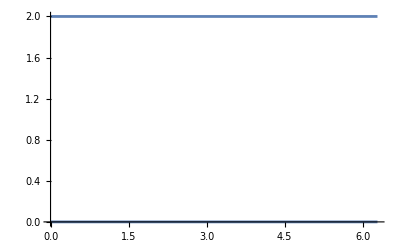

```mathematica
Plot[Eigenvalues[Cos[θ] PauliMatrix[1] - Sin[θ]  PauliMatrix[2] + IdentityMatrix[2]]  ,{θ,0,2Pi}]
```

```mathematica
Eigensystem[Cos[θ] PauliMatrix[1] - Sin[θ]  PauliMatrix[2]]
```

{{-1,1},{{-Cos[θ]-ⅈ Sin[θ],1},{Cos[θ]+ⅈ Sin[θ],1}}}